# Introdução à Física Computacional I (2023.2)

## Aula 6: gráficos; zeros e extremos de funções; ajustes de dados Capítulo 2.3.1

## Gráficos mais sofisticados

Já temos trabalhado com gráficos, mas agora vamos explorar como utilizar funções auxiliares e as opções da função Plot (e de outras funções a ela relacionadas) para melhorá-los.

Vamos primeiro voltar ao problema do período de um pêndulo de comprimento L abandonado de um ângulo inicial θ_0 com a vertical, período que é dado por T=√((8L)/g)∫_0^θ_0 (d θ)/(√(cosθ-cosθ_0)). O Mathematica “resolve” a integral em termos de integrais elípticas:

```mathematica
Integrate[1/Sqrt[Cos[θ]-Cos[θ0]],{θ,0,θ0},Assumptions->{0<θ0<π}]
```

(2 EllipticF[θ0/2,Csc[θ0/2]^2])/(√(1-Cos[θ0]))

Note a demora até a saída do cálculo anterior.

Quando traça um gráfico de uma função f, o Mathematica calcula “do zero” o valor da função em cada ponto, o que pode resultar em um grande tempo de cálculo para obter o gráfico completo. Nesses casos, é conveniente invocar a função Evaluate em combinação com a função Plot, o que força o cálculo do argumento de Evaluate antes de que se trace o gráfico:

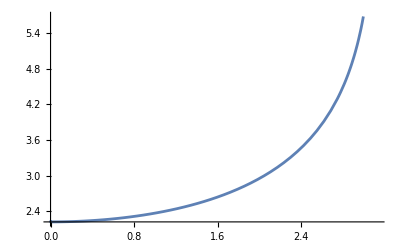

```mathematica
Plot[Evaluate[Integrate[1/Sqrt[Cos[θ]-Cos[θ0]],{θ,0,θ0},Assumptions->{0<θ0<π}]],{θ0,0,π-0.01}]
```

Não tente em casa executar a entrada anterior sem a função Evaluate, a menos que seu computador tenha uma memória gigantesca.

As opções da função Plot controlam, entre outras coisas, aspectos como cores das curvas, espessuras de linhas, tipos e tamanhos de fontes das legendas, a presença de uma moldura no gráfico etc. Para especificar uma opção, é preciso invocá-la como uma regra de transformação do tipo Nome→Valor, conforme os exemplos a seguir.

O potencial de Lennard-Jones fornece uma descrição razoável para a energia de interação entre dois átomos de um gás nobre cujos centros estão separados por uma distância r. Qualitativamente, sua forma funcional é

```mathematica
uLJ[r_]:=(1/r^12)-(1/r^6)
```

Vamos tentar traçar seu gráfico, mas já utilizando as  opções ImageSize→Large e LabelStyle→Large para aumentar o tamanho do gráfico e das legendas:

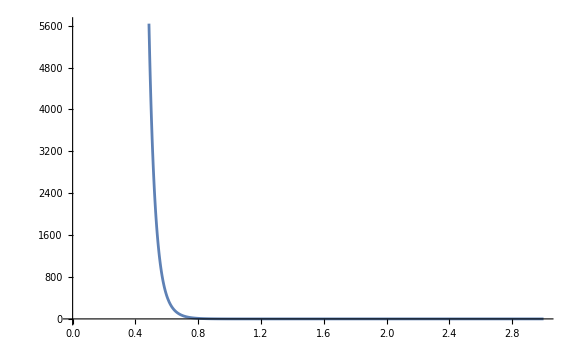

```mathematica
Plot[uLJ[r],{r,0.001,3.0},ImageSize->Large,LabelStyle-> Large]
```

Olhando muito atentamente, podemos suspeitar que há algum detalhe fino do gráfico em torno da abscissa igual a 1. Para verificar isso, calibramos o intervalo de valores das ordenadas com a opção PlotRange:

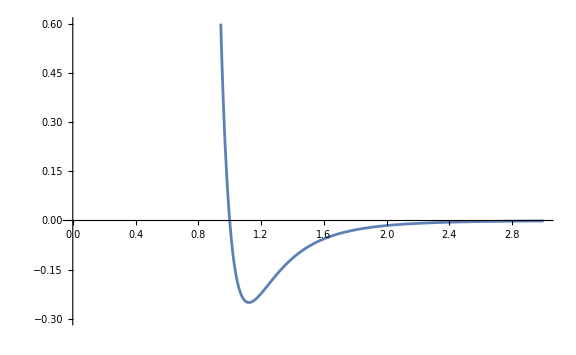

```mathematica
Plot[uLJ[r],{r,0.001,3.0},ImageSize->Large,LabelStyle->Large,PlotRange-> {-0.3,0.6}]
```

O Mathematica traça gráficos com número padrão de pontos igual a 50. Em certos casos, esse número pode ser insuficiente para reproduzir corretamente o comportamento da função. Por exemplo, considere o seguinte gráfico de batimentos, em que aproveitamos para ilustrar como padronizar opções com o uso da função Evaluate:

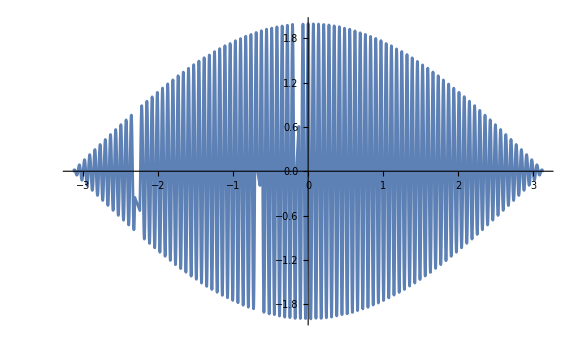
Null -Graphics-

```mathematica
optam={ImageSize->Large,LabelStyle->Large};(*Guarde as características gerais de gráficos em uma lista optam*)Plot[Cos[90*t]+Cos[91*t],{t,-π,π},Evaluate[optam]]
```

As falhas no gráfico resultam de uma amostragem insuficiente da função, que pode ser corrigida com o uso da opção PlotPoints. Note que agora também vamos associar o gráfico a uma variável:

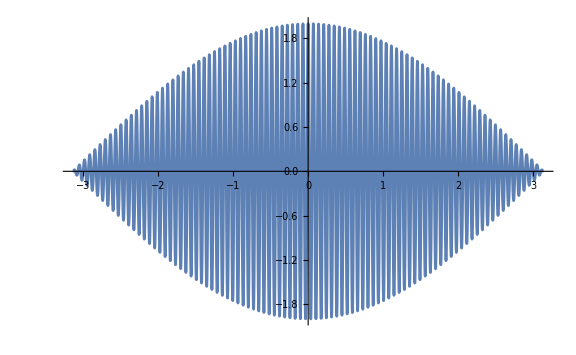

```mathematica
grafico1=Plot[Cos[90*t]+Cos[91*t],{t,-π,π},Evaluate[optam],PlotPoints-> 120]
```

Com o auxílio da função Show, podemos acrescentar (algumas) opções a um gráfico já traçado. Por exemplo, vamos rotular os eixos do gráfico anterior com a opção AxesLabel:

```mathematica
Show[grafico1,AxesLabel-> {"t (s)","y (A)"}]
```

Podemos remover os eixos e incluir uma moldura com as opções Axes→False e Frame→True:

```mathematica
Show[grafico1,Axes-> False,Frame-> True,FrameLabel-> {"t (s)","y (A)"}]
```

Note a substituição da opção AxesLabel por FrameLabel.

Para traçar o gráfico de uma função, não pode haver variáveis a que não tenham sido atribuídos valores. Em problemas físicos, uma forma de atribuir valores é adotar unidades convenientes ou, o que é equivalente, mudar para variáveis adimensionais. Vamos ilustrar essa estratégia com um problema de mecânica estatística.

Um sistema é composto de partículas não interagentes, cada uma das quais pode ter energia igual a 0 ou a ϵ, com esse último valor duplamente degenerado. Se o sistema é mantido a uma temperatura fixa T, suas propriedades termodinâmicas são obtidas da função de partição canônica Z=1+2 e^(-ϵ/(k T)), sendo k a constante de Boltzmann. A energia média por partícula e o calor específico são dados por
E=k T^2(∂ln Z)/(∂T)  e c=(∂E)/(∂T).
Vamos fazer gráficos dessas duas grandezas utilizando variáveis adimensionais, ou seja, vamos traçar E/ϵ e c/k em função da “temperatura reduzida” k T/ϵ:

```mathematica
Z=1+2*Exp[-ϵ/(k*T)]; (* Função de partição *)
energia=k*T^2*D[Log[Z],T]//Simplify (* Energia por partícula *)
calesp=D[energia,T] (* Calor específico *)
```

```mathematica
Plot[energia/ϵ/.{T-> t*ϵ/k},{t,0.01,4},AxesLabel->{"T (ϵ/k)","E (ϵ)"},Evaluate[optam]]
```

```mathematica
Plot[calesp/k/.{T-> t*ϵ/k},{t,0.01,4},AxesLabel->{"T (ϵ/k)","C (k)"},Evaluate[optam]]
```

Uma estratégia também válida, mas talvez fisicamente menos rica, é utilizar as regras de transformação ϵ→ 1 e k→ 1.

Quando queremos produzir múltiplos gráficos no mesmo conjunto de eixos, podemos tirar proveito de tabelas, como no exemplo a seguir.

A dependência da função de onda do elétron no átomo de hidrogênio com a distância até o núcleo vem da função radial 
R_(n,l)(r)=√(((n-l-1)!)/((n+l)! 2n))(2/na_0)^(3/2)(e^(-r/(na_0))((2r)/na_0))^l L_(n-l-1)^(2l+1)((2r)/na_0),
em que n=1,2,3,... é o número quântico principal, l=0,1,...,n-1 é o número quântico azimutal, a_0 é o raio de Bohr e L_k^j(x) é o polinômio de Laguerre generalizado (ou associado). A probabilidade de observar o elétron em uma distância contida no intervalo de largura dr em torno de r é [r R_(n,l)(r)]^2 dr. Para traçar a densidade de probabilidade (em unidades de 1/a_0) correspondente a (n,l)=(1,0), (2,0) e (3,0), em função de r (em unidades de a_0), fazemos

```mathematica
Rnl[n_,l_,r_]:=(2/(a*n))^(3/2)*Exp[-r/(n*a)]*Sqrt[((n-l-1)!)/(2*n*((n+l)!))]*(2*r/(n*a))^l*LaguerreL[n-l-1,2*l+1,2*r/(n*a)]
Plot[Evaluate[Table[(r*Rnl[n,0,r])^2/.a-> 1,{n,3}]],{r,0,25},PlotRange->{0,0.55},AxesLabel->{" r(a) "," P(r) (1/a) "},Evaluate[optam]]
```

Quando traçamos vários gráficos no mesmo conjunto de eixos, ajuda a visualização se preenchermos a área entre cada gráfico e o eixo com uma cor específica, usando a opção Filling→Axis. Além disso, podemos rotular cada gráfico, com a opção PlotLegends. Essas opções não podem ser acrescentadas com a função Show, de modo que temos que invocar novamente Plot:

```mathematica
Plot[Evaluate[Table[(r*Rnl[n,0,r])^2/.a-> 1,{n,3}]],{r,0,25},PlotRange->{0,0.55},AxesLabel->{"r (a)","P(r) (1/a)"}, Evaluate[optam],Filling-> Axis,PlotLegends-> {"n=1","n=2","n=3"}]
```

## Zeros e extremos de funções

Já discutimos a solução numérica de equações algébricas usando a função NSolve, que no entanto funciona quase que apenas para equações polinomiais. Em casos mais complicados, devemos utilizar a função FindRoot, que encontra uma solução por vez, a partir de um palpite inicial sobre essa solução.

O exemplo a seguir mostra uma função que tem dois zeros:

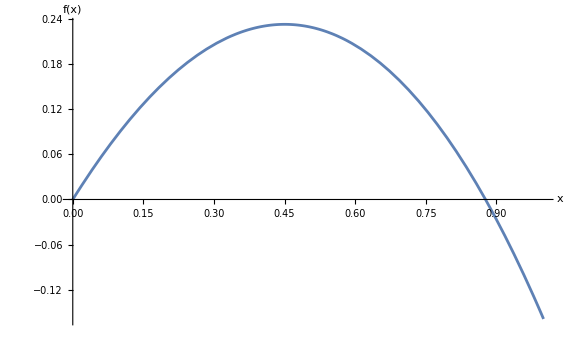

```mathematica
f[x_]:=Sin[x]-x^2 
grafico2=Plot[f[x],{x,0,1},Evaluate[optam],AxesLabel->{"x","f(x)"}]
```

Por inspeção visual, um dos zeros é próximo de x=0 e o outro, de x=0.9. Vamos determinar valores precisos desses zeros. Para isso, além de colocar a função a ser estudada, em uma mesma lista deve haver qual é a variável de interesse e uma estimativa para uma raíz

```mathematica
FindRoot[f[x]==0,{x,0.1}] (* Com palpite inicial igual a 0.1 *)
FindRoot[f[x]==0,{x,0.9}] (* Com palpite inicial igual a 0.9 *)
```

{x→-7.22011×10^-16}

{x→0.876726}

Uma maneira prática de estimar as posições dos zeros é utilizar a opção “Get Coordinates”, que surge ao clicarmos sobre o gráfico com o botão direito do mouse. Após selecioná-la, podemos clicar com o botão esquerdo sobre posições do gráfico próximas dos zeros, produzindo pontos coloridos a cada clique. Ao final, utilizar Ctrl-C (ou Cmd-C) copia as coordenadas desses pontos, que podem ser coladas a uma lista de pares ordenados:

```mathematica
Show[grafico2]
```

-Graphics-

```mathematica
lista= (* Cole ao lado a lista de pares ordenados *)
```

Em seguida, podemos construir uma tabela de soluções selecionando como palpite para a função FindRoot a coordenada x de cada par ordenado:

```mathematica
Table[FindRoot[f[x]==0,{x,lista[[i,1]]}],{i,Length[lista]}]
```

A função Length fornece o número de elementos de uma lista.

Para determinar extremos de funções, o Mathematica dispõe das funções FindMinimum e FindMaximum, cuja sintaxe é bastante semelhante à da função FindRoot.

Vamos ilustrar o uso dessas duas funções com o problema de um oscilador harmônico sujeito a uma força de resistência do ar proporcional ao quadrado da velocidade. A equação de movimento é x^(..)+2γ ẋ|ẋ|+ω_0^2 x=0, e vamos supor que o oscilador parte do repouso com uma deformação x_0=A. A solução numérica da equação de movimento com γ=0.2, ω_0=2 e A=1 (unidades arbitrárias) é obtida abaixo:

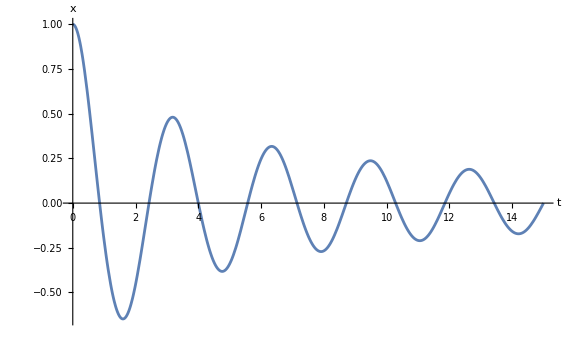

```mathematica
subs={γ-> 0.20,ω0-> 2,A-> 1}; 
sol=NDSolve[{x''[t]+2*γ*x'[t]*Abs[x'[t]]+ω0^2*x[t]==0,x[0]==A,x'[0]==0}/.subs,x,{t,0,15}];
pos[t_]:=x[t]/.sol[[1]]
Plot[pos[t],{t,0,15},AxesLabel->{"t","x"},Evaluate[optam]]
```

A partir do gráfico, vamos gerar uma lista de pares ordenados para localizar os mínimos e outra para localizar os máximos:

```mathematica
listamin={{1.5814404824955286,-0.6481409047717872},{4.686605472018176,-0.41878782783440704},{7.918143455300468,-0.2715910769641481},{11.041361729645919,-0.2236665534249942},{14.200686573636988,-0.1757420298858403}};
listamax=  {{3.1520762620796603,0.4780853983983331},{6.383614245361949,0.31719592651688755},{9.488779234884596,0.23503960044976613},{12.630050794052861,0.17342235589942523}};
```

Agora utilizamos FindMinimum e FindMaximum para produzir tabelas com as posições precisas dos extremos:

```mathematica
minimos=Table[FindMinimum[pos[t],{t,listamin[[i,1]]}],{i,Length[listamin]}]
maximos=Table[FindMaximum[pos[t],{t,listamax[[i,1]]}],{i,Length[listamax]}]
```

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{{-0.647967,{t→1.59869}},{-0.382044,{t→4.76125}},{-0.2712,{t→7.91156}},{-0.210273,{t→11.0579}},{-0.171719,{t→14.2026}}}

FindMaximum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient increase in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{{0.480452,{t→3.1827}},{0.317191,{t→6.33714}},{0.236875,{t→9.48505}},{0.189048,{t→12.6304}}}

## Gráficos e ajustes de dados

Já vimos que a função ListPlot permite traçar gráficos de dados experimentais organizados como uma listas de pares ordenados. Agora vamos explorar outras capacidades do Mathematica para lidar com esse tipo de gráfico.

Suponha que tenhamos registrado a posição de um carro (em metros) para diversos instantes de tempo (em segundos) e construído a lista e o gráfico abaixo:

```mathematica
dados={{0,0},{1,1.5},{2,6.0},{3,13.5},{4,24},{5,37.5},{6,54},{7,73.5},{8,96},{9,121.5}}; 
grafico3a=ListPlot[dados,PlotStyle->PointSize[0.025],AxesLabel->{"t (s)","d (m)"},Evaluate[optam]]
```

ListPlot::nonopt: Options expected (instead of optam) beyond position 1 in ListPlot[{{0,0},{1,1.5},{2,6.},{3,13.5},{4,24},{5,37.5},{6,54},{7,73.5},{8,96},{9,121.5}},PlotStyle→PointSize[0.025],AxesLabel→{t (s),d (m)},optam]. An option must be a rule or a list of rules.

ListPlot[{{0,0},{1,1.5},{2,6.},{3,13.5},{4,24},{5,37.5},{6,54},{7,73.5},{8,96},{9,121.5}},PlotStyle→PointSize[0.025],AxesLabel→{t (s),d (m)},optam]

Note o uso da opção PlotStyle→PointSize para controlar o tamanho do ponto utilizado no gráfico.

Agora vamos utilizar a função Fit para produzir um ajuste cúbico dos dados, por mínimos quadrados. Invocamos a função com os seguintes argumentos: (i) a lista que contém os dados a ajustar; (ii) uma lista indicando as funções 1, t, t^2 e t^3; (iii) a variável independente.

```mathematica
ajuste=Fit[dados,{1,t,t^2,t^3},t]
Chop[ajuste]
```

1.74428×10^-15+1.68356×10^-15 t+1.5 t^2-1.83177×10^-16 t^3

1.5 t^2

A função Chop elimina, por padrão, os termos numéricos de uma expressão que sejam menores do que 10^-10. Ajustes com outras funções podem ser feitos alterando o argumento (ii) de Fit.

Podemos produzir um gráfico da função de ajuste e combiná-lo com o gráfico dos dados usando a função Show:

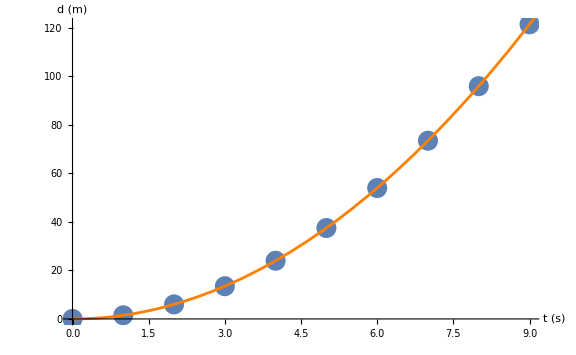

```mathematica
grafico3b=Plot[ajuste,{t,0,15},PlotStyle->Orange];
Show[grafico3a,grafico3b](*temos que usar o show pois s gráficos tem natureza distinta, um é plotlist e o outro é plot*)
```

Se quisermos traçar os dados utilizando linhas em vez de pontos, invocamos a função ListLinePlot:

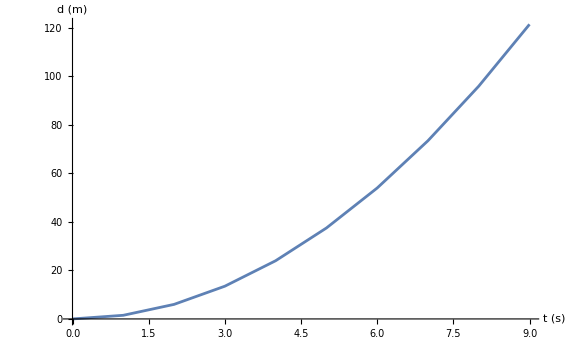

```mathematica
ListLinePlot[dados,AxesLabel->{"t (s)","d (m)"},Evaluate[optam]]
```

O padrão é unir os pontos por segmentos de reta. Para obter uma curva mais suave, existe a opção InterpolationOrder. Vamos interpolar os pontos com cúbicas:

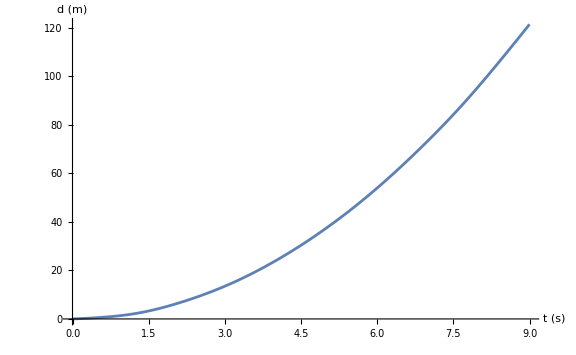

```mathematica
ListLinePlot[dados,AxesLabel->{"t (s)","d (m)"},Evaluate[optam],InterpolationOrder->3]
```

## Gráficos paramétricos

Para traçarmos gráficos bidimensionais de x(t) contra y(t), à medida que mudam os valores da variável independente t, invocamos a função ParametricPlot. Vamos ilustrá-la com o exemplo das figuras de Lissajous, produzidas a partir de x(t)=A_x cos(ω_x t+ϕ_x) e y(t)=A_y cos(ω_y t+ϕ_y). Isso pode corresponder, por exemplo, aos campos elétricos de duas ondas eletromagnéticas de polarizações perpendiculares que se combinam em um ponto.

```mathematica
fx[t_]:=ax*Cos[ωx*t+ϕx] 
fy[t_]:=ay*Cos[ωy*t+ϕy]
```

Primeiro um exemplo com a razão ω_x/ω_y igual a um número racional:

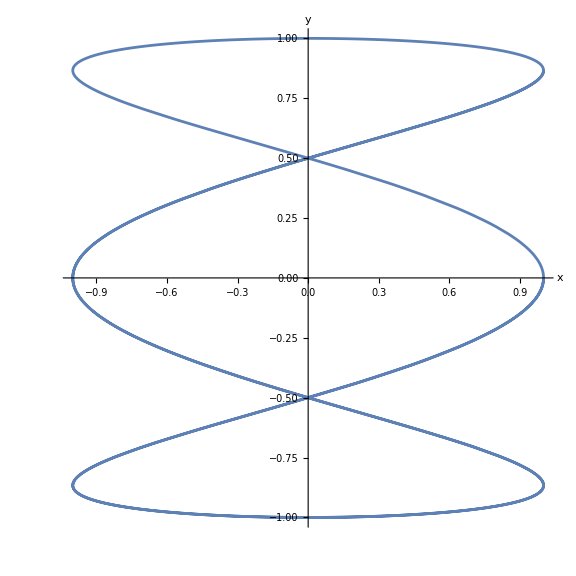

```mathematica
subs={ax-> 1,ay-> 1,ωx-> 1,ωy-> 1/3,ϕx-> 0,ϕy-> π/2}; 
ParametricPlot[{fx[t],fy[t]}/.subs,{t,0,10*π},AxesLabel-> {"x","y"},Evaluate[optam]]
```

Agora um exemplo com a razão ω_x/ω_y igual a um número irracional:

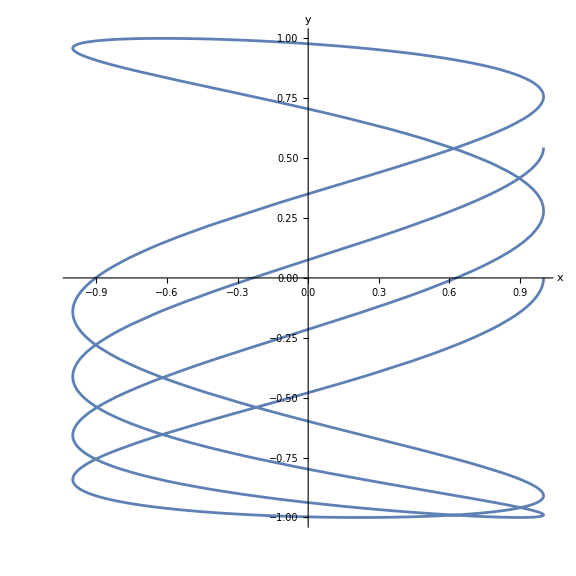

```mathematica
subs={ax-> 1,ay-> 1,ωx-> 1,ωy-> 1/π,ϕx-> 0,ϕy-> π/2};
ParametricPlot[{fx[t],fy[t]}/.subs,{t,0,10*π},AxesLabel-> {"x","y"},Evaluate[optam]]
```

Um último exemplo, agora a partir da solução numérica da equação de movimento de um oscilador amortecido:

```mathematica
subs={γ-> 0.20,ω0-> 2,A-> 1}; 
sol=NDSolve[{x''[t]+2*γ*x'[t]*Abs[x'[t]]+ω0^2*x[t]==0,x[0]==A,x'[0]==0}/.subs,x,{t,0,25}];
```

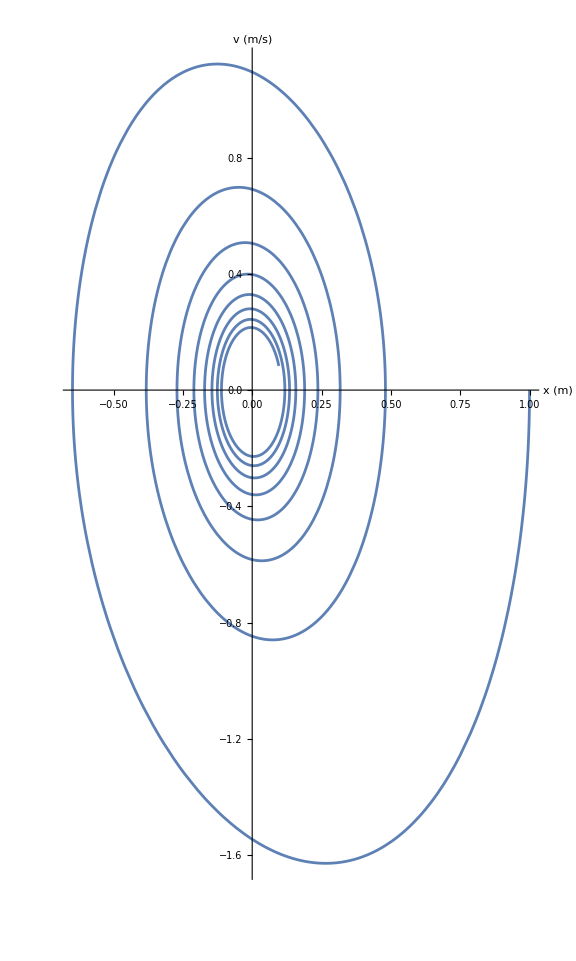

```mathematica
ParametricPlot[Evaluate[{x[t],x'[t]}/.sol],{t,0,25},AxesLabel-> {"x (m)","v (m/s)"},Evaluate[optam],PlotRange->All]
```

Esse é um gráfico do “espaço de fase” do oscilador. Note o uso da opção PlotRange→All para garantir que todos os pontos sejam mostrados.

## Exercícios no E-disciplinas